```mathematica
Directory[]
```

/home/dnaneet

Set current directory to notebook directory

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/dnaneet/ELC/data_collection_prj/pi_data_clustering

Import csv files

```mathematica
fn=FileNames["*.csv"]
dims=Dimensions[fn][[1]]
fn[[1]]
```

{December-16-2017.csv,December-18-2017.csv,December-19-2017.csv,January-11-2018.csv,January-19-2018.csv,January-22-2018.csv,January-23-2018.csv,January-24-2018.csv,January-25-2018.csv}

9

December-16-2017.csv

Number of sign-ins by day

{{3,5},{2,5},{3,5},{1,5},{6,5},{11,5},{15,5},{6,5},{21,5}}

{3,2,3,1,6,11,15,6,21}

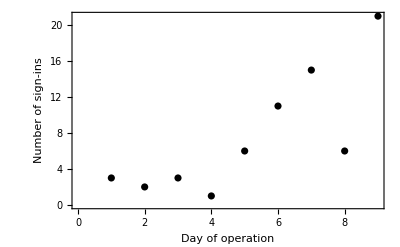

```mathematica
data=Table[Import[fn[[i]]],{i,1,dims,1}];
dimsDay=Table[Dimensions[data[[i]]],{i,1,dims}]

dimsDay[[All,1]]
ListPlot[dimsDay[[All,1]],Frame->True,BaseStyle->{FontSize->16},FrameLabel->{"Day of operation","Number of sign-ins"},FrameStyle->Black,PlotStyle->{Black}]
```

Sign - ins by course

{2,6,6,6,1,6,6,1,6,1,1,1,1,1,1,5,1,5,1,1,5,5,2,5,6,2,1,4,5,1,1,1,1,4,4,1,1,1,2,7,2,3,2,4,1,1,6,3,4,1,6,2,4,4,4,1,4,5,2,4,6,4,1,1,4,2,1,4}

{{2,9},{6,10},{1,26},{5,7},{4,13},{7,1},{3,2}}

{{1,Statics},{2,MoM},{3,Dyn},{4,ETF-1},{5,MATLAB},{6,SS},{7,fdbk.}}

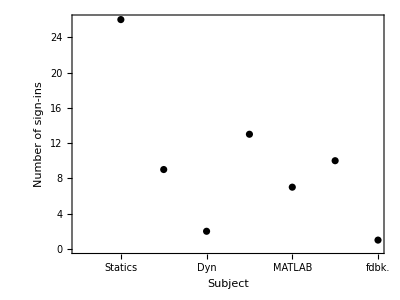

```mathematica
subjectData=Table[data[[i]][[All,1]],{i,1,dims,1}]//Flatten
tally=Tally[subjectData]
xTicks={"Statics", "Mechanics of Materials", "Dynamics", "ETF-1", "MATLAB", "Study Space", "Feedback"};
xTicks={{1,"Statics"}, {2,"MoM"}, {3,"Dyn"}, {4,"ETF-1"}, {5,"MATLAB"}, {6,"SS"}, {7,"fdbk."}}
ListPlot[tally,Frame->True,BaseStyle->{FontSize->12},FrameLabel->{"Subject","Number of sign-ins"},FrameStyle->Black,PlotStyle->{Black}
,
FrameTicks->{{Automatic,None},{xTicks,None}},AspectRatio->3/4]
```

Sign - ins by hour of day

{13,14,14,13,13,12,12,12,13,16,16,16,16,16,16,10,11,11,12,12,13,13,14,14,16,17,9,10,12,12,12,13,13,15,15,15,15,15,15,15,16,10,11,14,14,14,17,10,10,10,11,11,12,12,12,12,12,13,13,13,15,15,15,15,16,16,17,17}

{{13,11},{14,7},{12,13},{16,10},{10,6},{11,5},{17,4},{9,1},{15,11}}

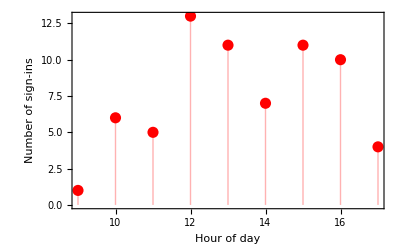

```mathematica
timeOfDay=Table[data[[i]][[All,5]],{i,1,dims,1}]//Flatten
tally=Tally[timeOfDay]
xTicks={"Statics", "Mechanics of Materials", "Dynamics", "ETF-1", "MATLAB", "Study Space", "Feedback"};
ListPlot[tally,Frame->True,BaseStyle->{FontSize->16},FrameLabel->{"Hour of day","Number of sign-ins"},FrameStyle->Black,PlotStyle->{Black,PointSize[0.02],Red},Filling->Axis]
```

Clustering of  course and time of day

{{2,13},{6,14},{6,14},{6,13},{1,13},{6,12},{6,12},{1,12},{6,13}}

{{{2,13}},{{6,14},{6,14}},{{6,13},{6,13}},{{1,13}},{{6,12},{6,12}},{{1,12}}}

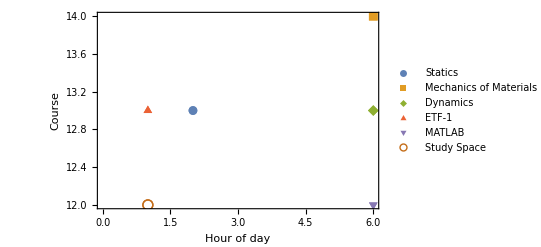

```mathematica
dataCT=Table[{subjectData[[i]],timeOfDay[[i]]},{i,1,dims,1}]
FindClusters[dataCT]
ListPlot[%,Frame->True,BaseStyle->{FontSize->16},FrameLabel->{"Hour of day","Course"},FrameStyle->Black,PlotLegends->{"Statics", "Mechanics of Materials", "Dynamics", "ETF-1", "MATLAB", "Study Space", "Feedback"},PlotMarkers->Automatic]
```

```mathematica
Example of find cluster
```

```mathematica
data={{-1.1,2.6},{3.9,-0.8},{4.2,-3.7},{3.3,3.5},{3.9,5.2},{4.1,-4.8},{3.8,3.7},{5.6,0.1},{3.1,-5.2},{-0.9,2.3},{2.9,4.1},{-2.3,3.9},{-2.5,3.},{2.6,-5.5},{5.2,1.9},{-0.7,1.3},{0.9,2.8},{-1.5,3.3},{3.8,1.2},{2.6,-5.1},{-0.8,3.2},{4.7,0.7},{3.,3.},{3.9,3.6},{4.5,1.4},{4.2,1.3},{-1.1,2.6},{4.8,2.4},{3.3,-3.5},{3.2,-4.6},{3.3,-4.9},{3.,3.5},{0.7,2.1},{3.2,-4.3},{-2.,0.5},{-1.2,2.},{-1.6,1.8},{-3.5,3.7},{4.8,0.2},{3.3,2.4},{-0.1,2.1},{-1.3,2.5},{4.4,3.9},{3.5,0.2},{0.1,2.9},{-1.,1.6},{-1.4,4.5},{3.2,2.5},{-1.6,2.4},{2.6,-5.1}};
```

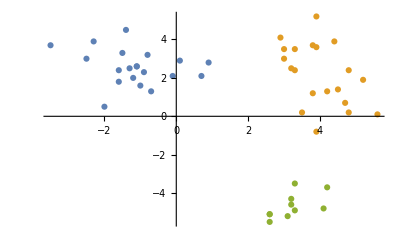

```mathematica
ListPlot[FindClusters[data]]
```